```mathematica
k=50;
```

```mathematica
costfunction[board_,weight_]:=Module[{team1,team2,zeroes,cost,me,min1,min2,cf},
COMPUTER=Position[board,1];
HUMAN=Position[board,2];
PTS=Nearest[Position[board,_?(#>0&)]];
cf=Total[Flatten[Table[
Table[
near=PTS[{i,j}];
If[Length[near]==2,
0,
near=near[[1]];
If[MemberQ[COMPUTER,near]==True,
weight[[near[[1]],near[[2]]]]
,
-weight[[near[[1]],near[[2]]]]
]
]
,{j,1,10}]
,{i,1,10}]]];
Return[cf];
]
```

```mathematica
AA=1;
BB=1;
```

```mathematica
GenBoards[board_,weight_,team_]:=Module[{boardtmp,options,moveoptions,set,set2},
options=Position[board,0];
If[team==1,set=1;set2=2;,set=2;set2=1;];
moveoptions=Table[
boardtmp=board;
boardtmp[[options[[i]][[1]]]][[options[[i]][[2]]]]=set;
boardtmp
,{i,1,Length[options]}];
Return[moveoptions];
]
```

```mathematica
(*grid=10;*)
grid=10;
TotalArea= grid^2;
board=Table[0,{grid},{grid}];
PS=Position[board,0];
weight=Table[i^AA j^BB,{i,1,grid},{j,1,grid}];
(*weight=Table[1,{i,1,grid},{j,1,grid}];*)
```

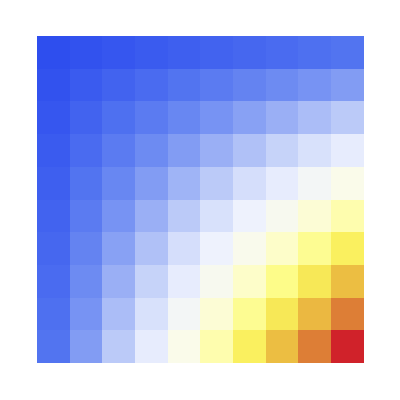

```mathematica
ArrayPlot[weight,ColorFunction->"TemperatureMap",PlotRangePadding->None]
```

### YOU GO FIRST

### Monte Carlo Tree Search

```mathematica
ALL={};
```

### Your Move

```mathematica
For[iteration=1,iteration≤2000,iteration++,
grid=10;
TotalArea= grid^2;
board=Table[0,{grid},{grid}];
PS=Position[board,0];
weight=Table[i^AA j^BB,{i,1,grid},{j,1,grid}];
RC=RandomChoice[Position[board,0]];
board[[RC[[1]]]][[RC[[2]]]]=2;
allboards=GenBoards[board,weight,1];
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;7]];
Table[tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;,{i,1,4}];
Table[tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;,{i,5,7}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
tc=Flatten[board];
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
froplot=Partition[toplot,grid];
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
AppendTo[ALL,{board,Flatten[froplot]/.{2->0,1->0}}];
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
RC=RandomChoice[Position[board,0]];
board[[RC[[1]]]][[RC[[2]]]]=2;
allboards=GenBoards[board,weight,1];
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;5]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,3}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,4,5}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
tc=Flatten[board];
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
froplot=Partition[toplot,grid];
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
AppendTo[ALL,{board,Flatten[froplot]/.{2->0,1->0}}];
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
RC=RandomChoice[Position[board,0]];
board[[RC[[1]]]][[RC[[2]]]]=2;
allboards=GenBoards[board,weight,1];
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;3]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,2}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,3,3}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
tc=Flatten[board];
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
froplot=Partition[toplot,grid];
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
AppendTo[ALL,{board,Flatten[froplot]/.{2->0,1->0}}];
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
RC=RandomChoice[Position[board,0]];
board[[RC[[1]]]][[RC[[2]]]]=2;
allboards=GenBoards[board,weight,1];
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;1]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,1}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
tc=Flatten[board];
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
froplot=Partition[toplot,grid];
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
AppendTo[ALL,{board,Flatten[froplot]/.{2->0,1->0}}];
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
]
```

$Aborted

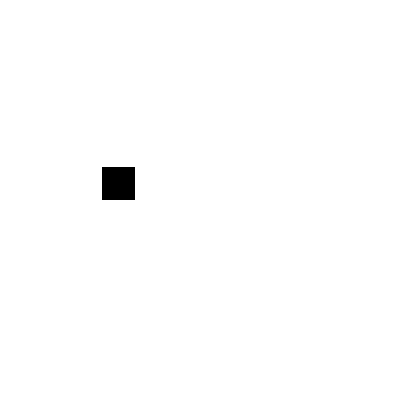

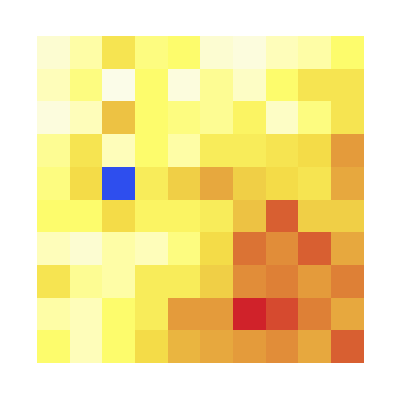

```mathematica
ArrayPlot[ALL[[1]][[1]]]
ArrayPlot[Partition[ALL[[1]][[2]],10],ColorFunction->"TemperatureMap"]
```

```mathematica
tf=Table[Flatten[{Flatten[ALL[[h]][[1]]],ALL[[h]][[2]]}]
,{h,1,Length[ALL]}];
```

```mathematica
(*tf=Import["~/Dropbox/tf.csv","CSV"];*)
```

```mathematica
Length[tf]
```

5612

```mathematica
ALL=Table[
a=Partition[tf[[i]][[1;;100]],10];
b=tf[[i]][[101;;]];
{a,b}
,{i,1,Length[tf]}];
```

```mathematica
DATA=Table[{ALL[[h]][[1]]}->ALL[[h]][[2]],{h,1,Length[ALL]}];
```

```mathematica
DATA[[12]][[2]]//Length
```

100

```mathematica
LL=Length[DATA]0.8//IntegerPart
```

4489

```mathematica
trainingData=DATA[[1;;LL]];
testData=DATA[[LL+1;;]];
```

```mathematica
(*NET=NetChain[{ConvolutionLayer[16,3],BatchNormalizationLayer[],Ramp,ConvolutionLayer[32,3],BatchNormalizationLayer[],Ramp,ConvolutionLayer[64,3],BatchNormalizationLayer[],Ramp,FlattenLayer[],DropoutLayer[],Ramp,500,DropoutLayer[],Ramp,100},"Output"->{100},"Input"->{1,10,10}]*)
```

```mathematica
window=100;
stepsize=1000;
counter = 0;
minloss=2345346546565556;
```

```mathematica
NET=Import["/Users/jordan/Dropbox/Net.wlnet"]
```

NetChain[<>]

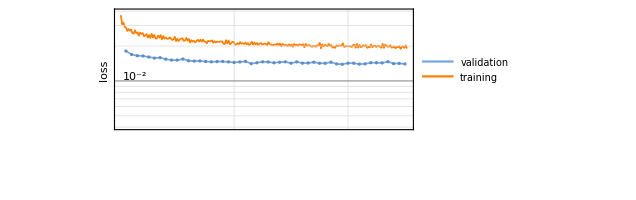
{NetChain[<>],-Graphics-}

```mathematica
{NET,LossEvolutionPlot}=NetTrain[NET,trainingData,{"TrainedNet","LossEvolutionPlot"},ValidationSet->testData,MaxTrainingRounds->1000,TargetDevice->"CPU"(*,BatchSize->6,TrainingProgressFunction->{If[#BatchLoss<6666666666666666666666(*minloss*),minloss=#BatchLoss;Print[#BatchLoss,"   ",#Round];
counter++;
Export["/scratch/ImagePredict13_128_"<>ToString[counter]<>".wlnet",#Net]]&,"Interval"->Quantity[stepsize,"Batches"]}*)]
```

```mathematica
TEST=Table[0,{10},{10}];
```

```mathematica
TEST[[1,1]]=1;
```

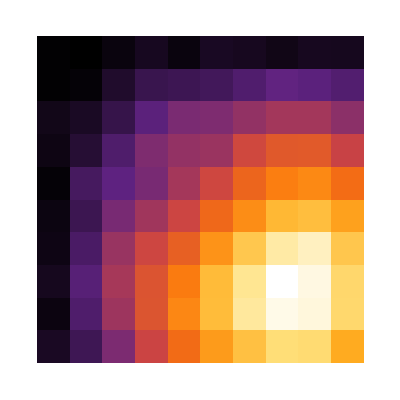

```mathematica
ArrayPlot[Partition[NET[{TEST}],10],ColorFunction->"SunsetColors",PlotRangePadding->None]
```

```mathematica
Export["~/Dropbox/Net_NEW.wlnet",NET]
```

~/Dropbox/Net_NEW.wlnet

```mathematica
Length[testData]
```

1241

```mathematica
pmap=(Blend[{{-0.0001,Purple},{0.0,Black},{0.0001,Purple},{0.36,Blue},{0.75,White},{0.9,RGBColor[1,0,0.5]},{1,RGBColor[1,0.5,0]}},#]&);
```

```mathematica
H=22;
```

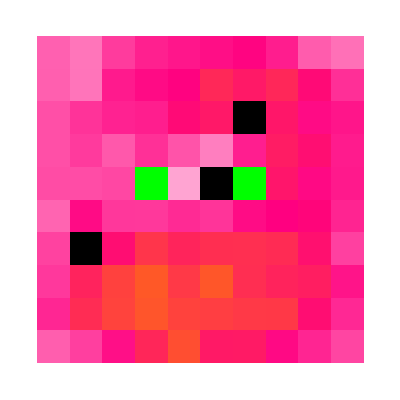

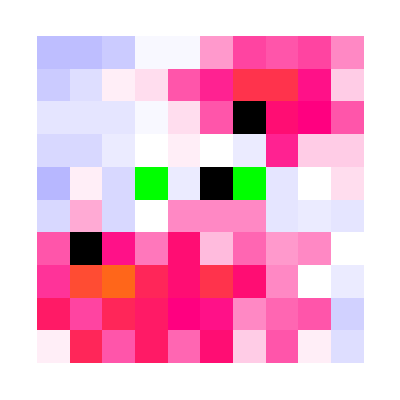

```mathematica
ArrayPlot[
Partition[NET[testData[[H]][[1]]],10](1-Sign[testData[[H]][[1]]][[1]])+(testData[[H]][[1]][[1]])
,PlotRangePadding->None,ColorFunctionScaling->False,ColorFunction->pmap,ColorRules->{1.->Green,2.->Black}]
ArrayPlot[
Partition[testData[[H]][[2]],10](1-Sign[testData[[H]][[1]]][[1]])+(testData[[H]][[1]][[1]])
,PlotRangePadding->None,ColorFunctionScaling->False,ColorFunction->pmap(*ColorData[{"RedBlueTones","Reverse"}]*),ColorRules->{1->Green,2->Black}]
```

```mathematica
4
```

```mathematica
LinearGradientImage[pmap]
```

-Graphics-

```mathematica
NET
```

NetChain[<>]

### Play

```mathematica
grid=10;
TotalArea= grid^2;
board=Table[0,{grid},{grid}];
PS=Position[board,0];
weight=Table[i j,{i,1,grid},{j,1,grid}];
```

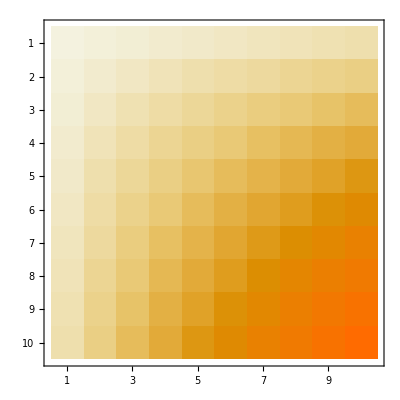

```mathematica
MatrixPlot[weight]
```

### You go first?

```mathematica
board[[8]][[8]]=2
```

2

```mathematica
costfunction[board,weight]//N
```

-6400.

### Machine go first

```mathematica
predicted=Partition[NET[{board}],10];
```

```mathematica
move=RandomChoice[Position[predicted,Max[predicted]]];
```

```mathematica
board[[move[[1]],move[[2]]]]=1;
```

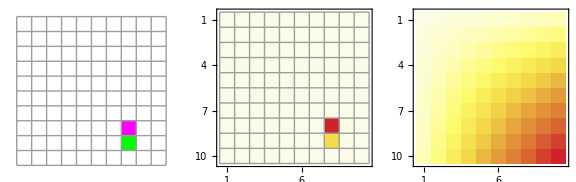

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
costfunction[board,weight]
```

-3680

```mathematica
board[[5]][[8]]=2
```

2

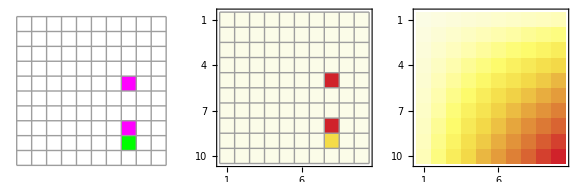

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
predicted=Partition[NET[{board}],10];
```

```mathematica
move=RandomChoice[Position[predicted,Max[predicted]]];
```

```mathematica
board[[move[[1]],move[[2]]]]=1;
```

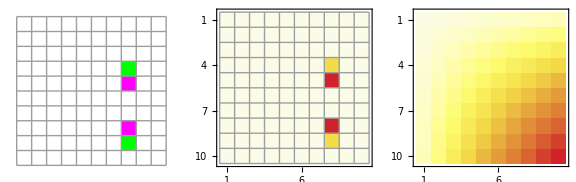

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
costfunction[board,weight]
```

640

```mathematica
board[[3]][[8]]=2
```

2

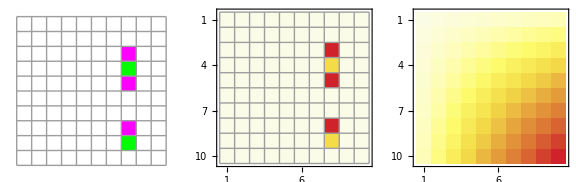

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
predicted=Partition[NET[{board}],10];
```

```mathematica
move=RandomChoice[Position[predicted,Max[predicted]]];
```

```mathematica
board[[move[[1]],move[[2]]]]=1;
```

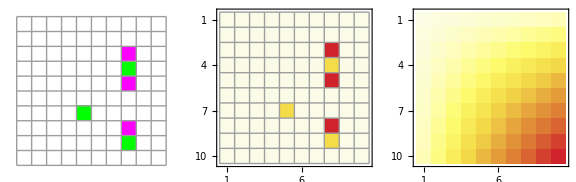

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
costfunction[board,weight]
```

937

```mathematica
board[[8]][[4]]=2
```

2

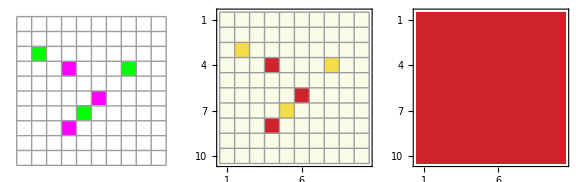

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
predicted=Partition[NET[{board}],10];
```

```mathematica
move=RandomChoice[Position[predicted,Max[predicted]]];
```

```mathematica
board[[move[[1]],move[[2]]]]=1;
```

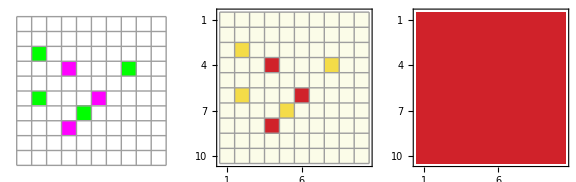

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[3]][[8]]=2
```

2

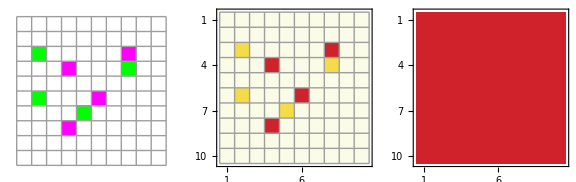

```mathematica
GraphicsRow[
{ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0],MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
costfunction[board_,weight_]:=Module[{team1,team2,zeroes,cost,me,min1,min2,cf},
COMPUTER=Position[board,1];
HUMAN=Position[board,2];
PTS=Nearest[Position[board,_?(#>0&)]];
cf=Total[Flatten[Table[
Table[
near=PTS[{i,j}];
If[Length[near]==2,
0,
near=near[[1]];
If[MemberQ[COMPUTER,near]==True,
-weight[[near[[1]],near[[2]]]]
,
weight[[near[[1]],near[[2]]]]
]
]
,{j,1,10}]
,{i,1,10}]]];
Return[cf];
]
```

```mathematica
costfunction[board,weight]
```

12

```mathematica
If[finalscore>0,Print[Style["MACHINE>MAN",Black,100]],Print[Style["MAN>MACHINE",Black,100]];
]
```

MACHINE>MAN